```mathematica
y={-1.48,-1.40, -1.16,-1.08,-1.02,0.14,0.51,0.53,0.078};
```

```mathematica
α=1;
σ1=0.1^2;
θ2=0;
σ2=1;
P["x|θ",{x_,θ1_}]:=PDF[NormalDistribution[θ1,σ1]][x]
P["θ",{θ_}]:=PDF[NormalDistribution[θ2,σ2]][θ]
P["θ|x",{θ_,x_}]=(P["x|θ",{x,θ}]P["θ",{θ}])/(∫_(-∞)^(+∞) P["x|θ",{x,s}]P["θ",{s}]ⅆs)
r[x_]=α∫_(-∞)^(+∞) P["x|θ",{x,θ}]P["θ",{θ}]ⅆθ
ParamUpdate[x_]:=(σ/.Solve[P["θ|x",{x,x}]==PDF[NormalDistribution[x,σ]][x],{σ}])[[1]]
```

39.8962 ⅇ^(0.49995 x^2-5000. (x-θ)^2-θ^2/2)

0.398922 ⅇ^(-0.49995 x^2)

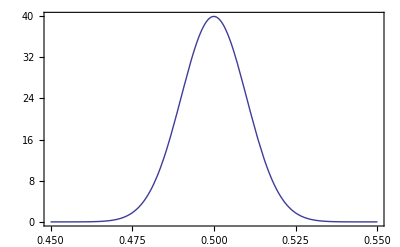

```mathematica
Plot[P["θ|x",{θ,0.5}],{θ,0.45,0.55},PlotRange->All,Frame->True]
```

```mathematica
Sample[x_,θ_,i_]:=Module[{mT,θn,q,b,μ,σ},
θn=Delete[θ,i];
mT=Length[θn];
q=Plus@@Table[P["x|θ",{x[[i]],θn[[j]]}],{j,1,mT}];
b=1/(q+r[x[[i]]]);
μ=x[[i]];
σ=ParamUpdate[μ];
If[Random[]<b q,θ[[RandomInteger[{1,mT}]]],
RandomVariate[NormalDistribution[μ,σ],1][[1]]]]
```

```mathematica
GibbsSampler[x_,n_,m_]:=Module[{N,θ,r},
N=Length[x];
θ=Table[Random[],{N}];
Do[Do[θ[[i]]=Sample[x,θ,i],{i,1,N}],{m}];
r=Table[0,{n},{N}];r[[1]]=θ;
Do[Do[θ[[i]]=Sample[x,θ,i],{i,1,N}];r[[k+1]]=θ,{k,1,n-1}];
r]
```

```mathematica
data=GibbsSampler[y,1000,500];
```

```mathematica
density[data_,F_]:=Module[{N},
N=Length[data];
Table[1/N Plus@@Map[F,data[[All,i]]],{i,1,Length[data[[1]]]}]]
```

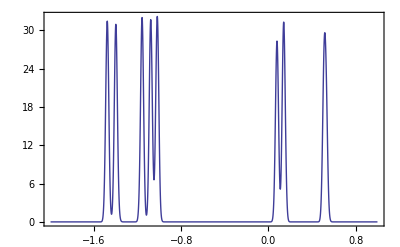

```mathematica
Plot[Plus@@density[data,P["x|θ",{x,#}]&],{x,-2,1},PlotRange->All,Frame->True]
```

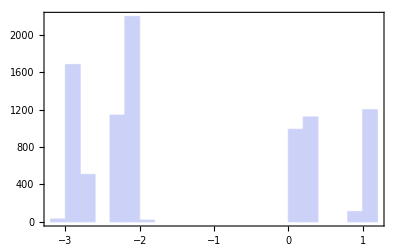

```mathematica
Histogram[2Flatten[data],Frame->True]
```

```mathematica
data=GibbsSampler[y,1000,100];
```

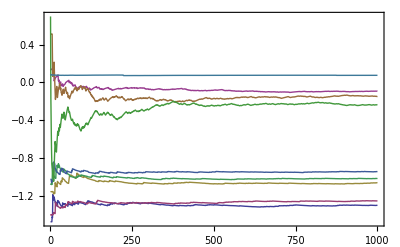

```mathematica
ListPlot[Transpose[data],Frame->True,Joined->True]
```

```mathematica
data=GibbsSampler[y,1000,1000];
```

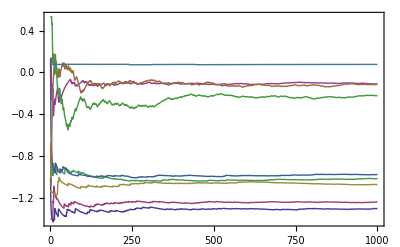

```mathematica
ListPlot[Transpose[data],Frame->True,Joined->True]
```

```mathematica
data=GibbsSampler[y,10000,100];
```

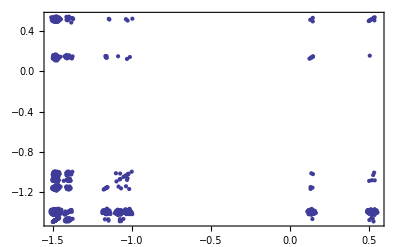

```mathematica
ListPlot[data[[All,{1,2}]][[-5000;;-1]],Frame->True,PlotRange->All]
```